Assignment 1

### Question 9

```mathematica
ClearAll["Global`*"]
```

```mathematica
Rp= {Vp*Cos[αp]*t,(Yp0 - Vp*Sin[αp]*t)};
Rt= {Xt0+Vt*t,0};
R = Rp-Rt;
R2= FullSimplify[{R}.Transpose[{R}]];
Rdot= FullSimplify[D[R2,t]];
tmiss = Solve[Rdot==ConstantArray[0,{1,1}],t]
```

{{t→(-Vt Xt0+Vp Xt0 Cos[αp]+Vp Yp0 Sin[αp])/(Vp^2+Vt^2-2 Vp Vt Cos[αp])}}

```mathematica
Rmiss = FullSimplify[R/.tmiss]
```

{{(Vp Sin[αp] (-Vt Yp0+Vp Yp0 Cos[αp]-Vp Xt0 Sin[αp]))/(Vp^2+Vt^2-2 Vp Vt Cos[αp]),Yp0-(Vp Sin[αp] (-Vt Xt0+Vp Xt0 Cos[αp]+Vp Yp0 Sin[αp]))/(Vp^2+Vt^2-2 Vp Vt Cos[αp])}}

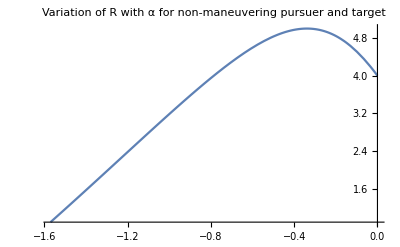

```mathematica
Rmiss = FullSimplify[Rmiss/.{Xt0->3,Yp0->4,Vp->2Vt}];
Rmag = (FullSimplify[Rmiss.Transpose[Rmiss]][[1,1]])^.5;
Plot[Rmag,{αp,-π/2,0},PlotLabel->"Variation of R with α for non-maneuvering pursuer and target"]
```

### Question 11

```mathematica
ClearAll["Global`*"]
```

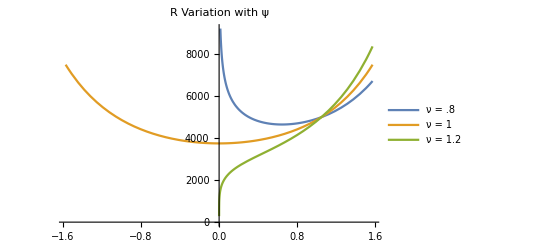

```mathematica
c = (R0 *Sin[ψ0]/(Tan[ψ0/2]^ν))/.{ψ0 ->π/3,R0->5000};
R = (c*Tan[ψ/2]^ν)/Sin[ψ];
Plot[{R/.{ν->.8}, R/.{ν->1},R/.{ν->1.2}}, {ψ,-π/2,π/2},PlotLegends->{"ν = .8", "ν = 1","ν = 1.2"},PlotLabel->"R Variation with ψ"]
```

### Question 12 Pure Pursuit

```mathematica
ClearAll["Global`*"]
```

```mathematica
vT = 300;
αT = 170*(π/180);
θ0=π/6;
vM =ν *vT;
R0 = 3000;
```

```mathematica
tf = (R0 *( vT* Cos[αT - θ0] + vM))/(vM^2-vT^2);
tmiss = (2*vM*Rmiss-  R0 *(vT Cos[αT - θ0] + vM))/(vT^2-vM^2);
c = (R0 *(1+Cos[αT-θ0])^ν)/(Sin[αT-θ0]^(ν-1));
Rmiss = (c*(Sin[ArcCos[ν]]^(ν-1)))/((1+ν)^ν);
```

```mathematica
νs = {0.9,1.5,3}
```

{0.9,1.5,3}

For ν = 0.9 :

Time of flight is -7.05029

Rmiss (Miss Distance) is 473.513

tmiss (Time at Miss Distance) is 7.90276

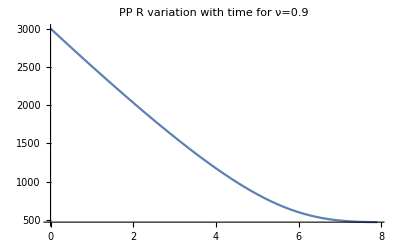

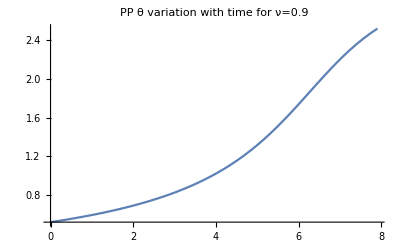

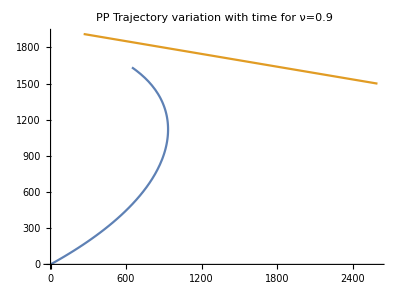

For ν = 1.5 :

Time of flight is 5.87164

Rmiss (Miss Distance) is 80.0922+80.0922 ⅈ

tmiss (Time at Miss Distance) is 5.23091-0.640737 ⅈ

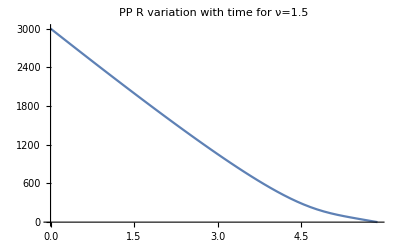

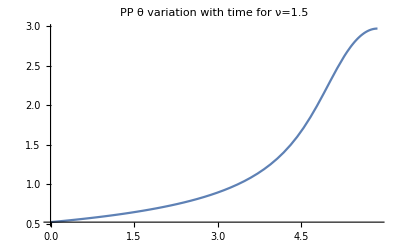

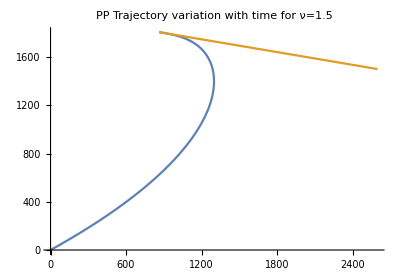

For ν = 3 :

Time of flight is 2.79244

Rmiss (Miss Distance) is -11.6224

tmiss (Time at Miss Distance) is 2.8215

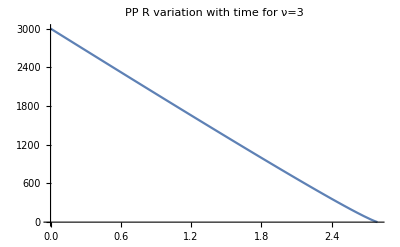

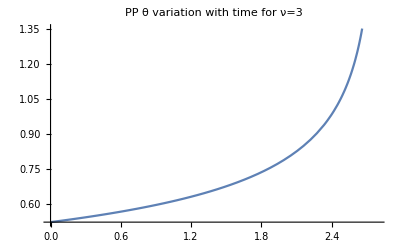

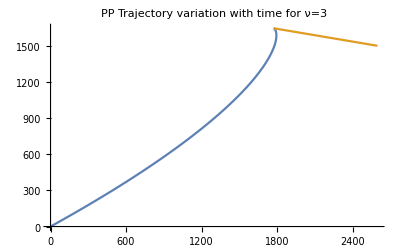

```mathematica
For[i=1,i≤Dimensions[νs][[1]],i++,
Print["For ν = ",νs[[i]]," :"];
tfi = N[tf/.{ν->νs[[i]]}];
Print["Time of flight is ",tfi];
Print["Rmiss (Miss Distance) is ",N[Rmiss/.{ν->νs[[i]]}]];
tmissi = N[tmiss/.{ν->νs[[i]]}];
Print["tmiss (Time at Miss Distance) is ",tmissi];
If[tfi>0,tendi = tfi,tendi = Re[tmissi]];
sol = NDSolve[{R'[t]==((vT* Cos[αT-θ[t]] )-vT*νs[[i]]),θ'[t]== ((vT* Sin[αT-θ[t]])/R[t]),x'[t]==(vT*νs[[i]]*Cos[θ[t]]),y'[t]==(vT*νs[[i]]*Sin[θ[t]]) ,R[0]==R0, θ[0]==θ0, x[0]==y[0]==0},{R,θ,x,y},{t,0,tendi}];
Print[Plot[Evaluate[R[t]/.sol],{t,0,tendi},PlotLabel->ToString[StringForm["PP R variation with time for ν=``",νs[[i]]]]]];
Print[Plot[Evaluate[θ[t]/.sol],{t,0,tendi},PlotLabel->ToString[StringForm["PP θ variation with time for ν=``",νs[[i]]]]]];
Print[ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{R0 *Cos[θ0] + vT *t *Cos[αT],R0 *Sin[θ0] + vT *t* Sin[αT]}}, {t,0,tendi},PlotLabel->ToString[StringForm["PP Trajectory variation with time for ν=``",νs[[i]]]]]];
Print[""];
]
```

### Deviated Pure Pursuit

```mathematica
ClearAll["Global`*"]
```

```mathematica
vT = 300;
αT = 170*(π/180);
θ0=π/6;
vM =ν *vT;
R0 = 3000;
δ = 25*(π/180);
```

```mathematica
vR0  = vT*Cos[αT-θ0]-vM*Cos[δ];
vθ0 = vT *Sin[αT-θ0] - vM *Sin[δ];
tf = (R0 *(vR0 + 2 vM *Cos[δ] - vθ0 *Tan[δ]))/(vM^2-vT^2);
tmiss = (2*vM*Rmiss-  R0 *(vT Cos[αT - θ0] + vM))/(vT^2-vM^2);
c = (R0 *(1+Cos[αT-θ0])^ν)/(Sin[αT-θ0]^(ν-1));
Rmiss = (c*(Sin[ArcCos[ν]]^(ν-1)))/((1+ν)^ν);
```

```mathematica
νs = {0.9,1.5,3}
```

{0.9,1.5,3}

For ν = 0.9 :

Time of flight is 3.82848

Rmiss (Miss Distance) is 473.513

tmiss (Time at Miss Distance) is 7.90276

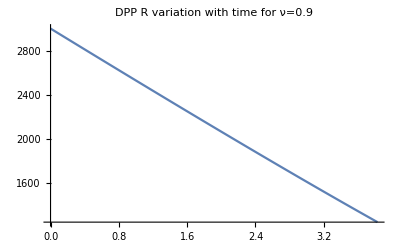

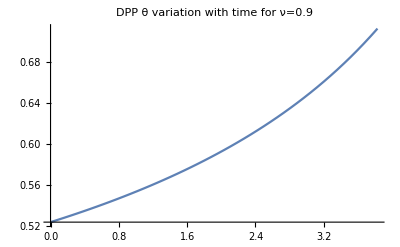

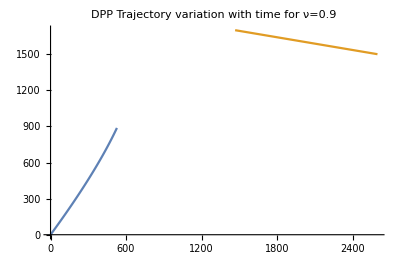

For ν = 1.5 :

Time of flight is 4.71429

Rmiss (Miss Distance) is 80.0922+80.0922 ⅈ

tmiss (Time at Miss Distance) is 5.23091-0.640737 ⅈ

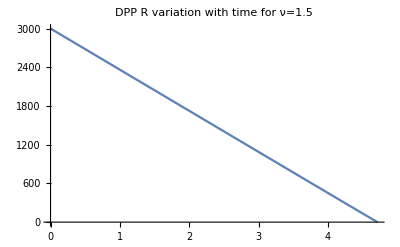

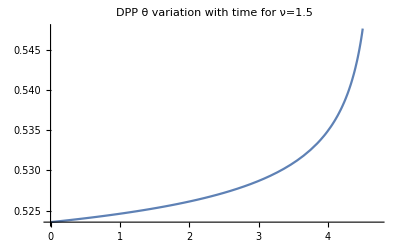

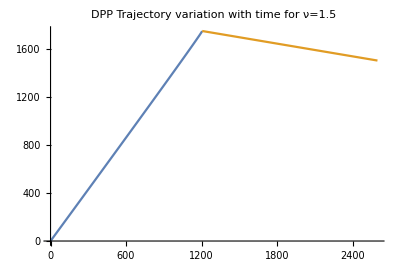

For ν = 3 :

Time of flight is 2.80544

Rmiss (Miss Distance) is -11.6224

tmiss (Time at Miss Distance) is 2.8215

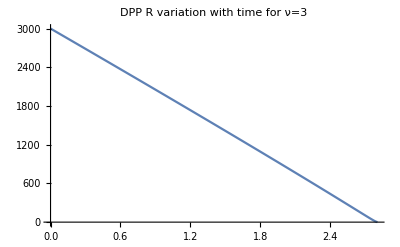

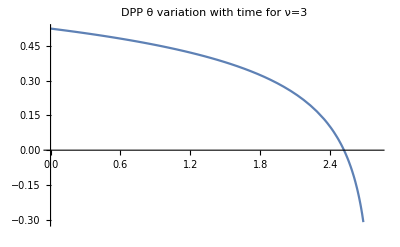

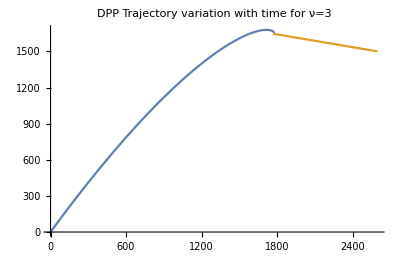

```mathematica
For[i=1,i≤Dimensions[νs][[1]],i++,
Print["For ν = ",νs[[i]]," :"];
tfi = N[tf/.{ν->νs[[i]]}];
Print["Time of flight is ",tfi];
Print["Rmiss (Miss Distance) is ",N[Rmiss/.{ν->νs[[i]]}]];
tmissi = N[tmiss/.{ν->νs[[i]]}];
Print["tmiss (Time at Miss Distance) is ",tmissi];
If[tfi>0,tendi = tfi,tendi = Re[tmissi]];
sol = NDSolve[{R'[t]==((vT* Cos[αT-θ[t]] )-vT*νs[[i]]*Cos[δ]),θ'[t]== ((vT* Sin[αT-θ[t]]-vT*νs[[i]]*Sin[δ])/R[t]),x'[t]==(vT*νs[[i]]*Cos[θ[t]+δ]),y'[t]==(vT*νs[[i]]*Sin[θ[t]+δ]) ,R[0]==R0, θ[0]==θ0, x[0]==y[0]==0},{R,θ,x,y},{t,0,tendi}];
Print[Plot[Evaluate[R[t]/.sol],{t,0,tendi},PlotLabel->ToString[StringForm["DPP R variation with time for ν=``",νs[[i]]]]]];
Print[Plot[Evaluate[θ[t]/.sol],{t,0,tendi},PlotLabel->ToString[StringForm["DPP θ variation with time for ν=``",νs[[i]]]]]];
Print[ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{R0 *Cos[θ0] + vT *t *Cos[αT],R0 *Sin[θ0] + vT *t* Sin[αT]}}, {t,0,tendi},PlotLabel->ToString[StringForm["DPP Trajectory variation with time for ν=``",νs[[i]]]]]];
Print[""];
]
```

Assignment 2

### LOS Maneuvering Target

```mathematica
ClearAll["Global`*"]
```

```mathematica
R = 1;
xT = R*Cos[t];
yT = R*Sin[t];
xP = 2*R*Sin[t]*Cos[t];
yP = 2*R*Sin[t]*Sin[t];
```

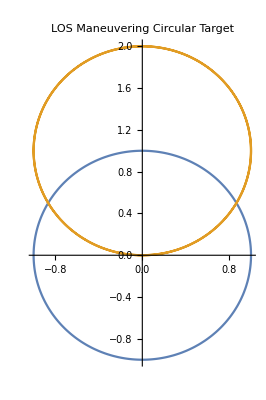

```mathematica
ParametricPlot[{{xT,yT},{xP,yP}}, {t,0,2*π},PlotLabel->"LOS Maneuvering Circular Target"]
```